Project Title

Bhattacharya, Bhubanjyoti

Espigulé, Bernat

Wayne State University, Detroit, MI (USA)

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: Analyzing special characters in papers on arXiv.org

SUMMARY OF WORK:  We took data from “. Our primary goal was to find the frequency of special characters (like Greek alphabets and/or mathematical symbols) in any arXiv article, and to study this as a function of time, finding periods of growth, stability, and decline of usage. From the corpus we created a Dataset containing: {Year and Month,Type,Number,Title,Symbols} from each paper. We used the Dataset to analyze the frequency of symbols in different arXiv types. As a visualization tool we used WordClouds and DateListStepPlot. The figure shows the distribution of cumulative symbol frequencies in different arXiv types, from 1998/01 to 2006/12. We used Classify on a portion of our dataset to classify articles by arXiv category. We checked the performance of our classifier on a part of the data finding a low success rate, and concluded that our classifier function needs further input.

RESULTS AND FUTURE  WORK: We constructed a database containing symbols and titles from arXiv.org articles. We used it to visualize the frequency distribution of symbols. Although, our effort to use the Classify function and predict the type of arXiv from an article’s title and symbols did not work so well, as a future objective we wish to expand the database to include key words from the articles that are closely related to the symbols and construct a probability function for obtaining arXiv type given the symbols in an article.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

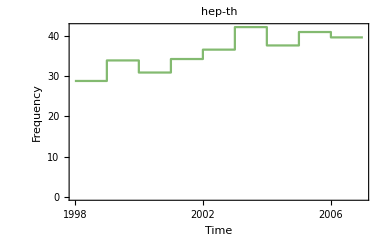
-Graphics--Graphics--Graphics--Graphics- 
Variation of frequencies in astro-ph arXives over many years

-Graphics-"α"-Graphics-

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

The most important result of this project was the creation of a database of symbols extracted from individual papers on arXiv.org. The database file is available at  .
The database file contains a Wolfram Language Dataset in “.mx” format. The database contains information from papers in the following format: {“YearMonth”, ”Type”, “Number”, “Title, “Symbols”} where the entry under “Symbols” is an association containing the symbol as a Key and its frequency as the Value.

In addition to creating the database, we analyzed the data and created plots for visualizing it. We plotted the frequency of the symbol “α” in each arXiv as a function of time. Although we expected to find features in these plots, we found stable plots showing the near uniform use of these symbols in the different arXives.

We selected a small subset of the full data set and used the WL function Classify on it with the idea of classifying the data by arXiv types based on the symbols that appeared in an article and the non “stop”-words that appeared in its title. Upon testing our classifier on another subset of the data set it performed dismally. Out of 881 cases tried, in 319 the classifier was successful in predicting the arXiv type, i.e. a success rate of about 36%. This test showed the Classify function needs more structured input.

Our follow-up plan for the project is to include definition words for each symbol from the source files. This would eventually help us create a comprehensive database that can be used as the basis for a dictionary for the usage of each symbol.

Code

Provide one of:

Link to the GitHub:

Explicit code (please access the explicit code posted in notebooks from the GitHub page above)

Written Content / Lesson Plans

As part of this project we maintained a record of steps taken during the course of the project. This is available in markdown format here:

Conclusions in Detail

In our project, although we expected to see some structure in the Frequency plots for a symbol (we used “α” as the test symbol in this project) in different arXives, we barely saw any structure. While we found that the most popular symbol has changed in the different categories of arXives, the frequency of usage of “α” (normalized to the number of papers published during some period) has remained mostly flat over time. We did find that the usage frequency for “α” depended on the type of arXiv, for example in “hep-ph” the frequency has hovered around a lower value than in “hep-th” where the frequency also seems to have grown slightly over the years.

Due to limited availability of time and memory space, we limited ourselves to a fraction (about a tenth) of the available data. If we include all of the available data, there is a possibility of seeing more structure. There is therefore need for careful curation of the data from the arXives.

We also concluded that there is need for further analyses of the body of each source file to extract words that can establish definitions for each symbol. This will help us set up a dictionary for the different possible meanings of each symbol.

All Visualizations

All the visualizations that were created in this project can be viewed at the following location:   .

Data Sources Links/References

We thankfully acknowledge use of the following data source:

Mathematical REtrieval Collection (MREC), based on arXMLiv a project of Prof. Dr. Michael Kohlhase’s group at Jacobs University Bremen.

Future Directions

The next step clearly is to make a direct connection between the symbols in an article, and its contents. The idea would be to grab words on either side of an “inline” symbol to establish a connection between the symbol and the material of the paper. At the same time these words may serve as a dictionary for the symbols. Once such a dictionary is included in the database, one may associate a probability for an article to belong to a certain type given the symbols in it and the dictionary associated with the symbols. At that stage it would be possible to predict subject matter in an article using its symbol content.

Background Info Links/References

We thankfully acknowledge use of the following resources:

Giorgia Fortuna, “2 Pi or Not 2 Pi”, blog posted on

Conversations with Stephen Wolfram about the creation of a dictionary for symbols using the Wolfram Language and defining a probability function for arXiv type based on symbols, among other directions for this study.

Conversations with Bernat Espigule regarding Clustering Trees, Dendrograms, creating a database using Dataset, and other directions in this study.

Keywords

Provide keywords as items

arXiv, MREC

XML, XHTML

special characters, α, β, ...

scientific definitions

Dataset, WordCloud, DateListPlot, DateListStepPlot, ClusteringTree

Other

Github repository containing this notebook: 
Github link to this notebook:

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```